```mathematica
Get[NotebookDirectory[]<>"/tzor/tzor.m"]
```

Tzór for Theorized package of sum rules.

Get Lastest Version : [Tzor@github](https://github.com/amapoplar/Tzor)

Author : poplar, xlchen, zzchen, dklian

Version : alpha

Lastest Veresion : This Version

```mathematica
Clear[classifyAmp]
giveParaProgSets[FeynAmpD[lists__?ListQ]]:={lists};
giveParaProgSets[a_ b_]:=Join[giveParaProgSets[a],giveParaProgSets[b]];
giveParaProgSets[a_]:={Nothing};
giveMomentum[slash[p_],p_]:=1
giveMomentum[scalarP[p_,p_],p_]:=2
giveMomentum[scalarP[p_,x_],p_]:=1
giveMomentum[fourVector[p_,μ_],p_]:=1
giveMomentum[a_  b_,p_]:= giveMomentum[a,p]+ giveMomentum[b,p]
giveMomentum[a_^n_,p_]:= n giveMomentum[a,p]
giveMomentum[a__]:=0

classifyAmp[exp0_?(MemberQ[Level[#,Infinity,Heads->True],FeynAmpD]&)] := Module[{exp =exp0,listk,listn,listp,listreplace,symbolf},
listk = Transpose[giveParaProgSets[exp]];
listp = giveMomentum[exp,symbol[#]#]&/@listk[[1]];
listk = Transpose[Join[{listp},listk]];
listk = SortBy[listk,{Last,First}];
listn = ToExpression["♉"<>ToString[#]]&/@Range[Length[listk]];
listreplace  = Table[symbol[listk[[;;,2]][[i]]]listk[[;;,2]][[i]]->symbol[listk[[;;,2]][[i]]]listn[[i]],{i,Length[listk]}];
showYourIndices[exp/.listreplace,listn]
]
ggg scalarP[k1,p] scalarP[k1, k2]scalarP[k2,k3]scalarP[k3,k4]FeynAmpD[{k1, mass[c],4}, {-k2, mass[c], 3}, 
   {-k3, mass[c],7}, {-k4, mass[c], 6}]
classifyAmp[%]
```

ggg k2·k1 p·k1 k3·k2 k4·k3 1/((k1^2-m_c^2)^4·(k2^2-m_c^2)^3·(k3^2-m_c^2)^7·(k4^2-m_c^2)^6)

-ggg p_p0 (♉1)_(♉10) (♉1)_(♉11) (♉2)_(♉20) (♉2)_(♉21) (♉3)_(♉30) (♉4)_(♉40) (♉4)_(♉41) g_(p0♉20) g_(♉10♉21) g_(♉11♉40) g_(♉30♉41) 1/(((♉1)^2-m_c^2)^3·((♉2)^2-m_c^2)^4·((♉3)^2-m_c^2)^6·((♉4)^2-m_c^2)^7)

```mathematica
scalarP[-p,x]
```

-(x·p)

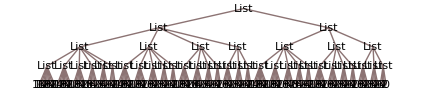

```mathematica
ls = {};
Fold[Range[#1+#2,0,-2]&,0,{2,5,3,6}]//TreeForm
```

```mathematica
ls
```

{{{{10,8,6,4,2,0},{8,6,4,2,0},{6,4,2,0}},{{8,6,4,2,0},{6,4,2,0}}},6}

```mathematica
16*9
```

144

```mathematica
genVector[q_,lists_?ListQ]:= Times@@(fourVector[q,#]&/@lists)
subPartition[lists_?ListQ,n_?NumberQ]:={ #,Complement[lists,#]}&/@Subsets[lists,{n}]
genMetric[lists_?ListQ]:=Times@@(metric[#[[1]],#[[2]]]&/@Partition[lists,2])
genMetrick[lists_?ListQ,n_?NumberQ]:=Module[{},
Plus@@(genVector[ToExpression["q"],#[[1]]]genMetric[#[[2]]]&/@subPartition[lists,n])
]
genStruct[lists_?ListQ]:=Module[{n = Length[lists]},
Plus@@(genMetrick[lists,#]&/@Range[n,0,-2])
]
Table[genStruct[Range[i]]//Length,{i,16}]
```

{2,2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768}

```mathematica
genStruct[Range[12]]
```

```mathematica
indexNew["μ","EndQ"-> True]
indexNew["μ","EndQ"-> True]
indexNew["μ","EndQ"-> True]
indexNew["ν","EndQ"-> True]
```

μ6

μ7

μ8

ν2

```mathematica
indexNew["♉"]
```

♉0

```mathematica
showYourIndices[exp_,lists_?ListQ]:=Module[{explists = FactorList[exp],countnum = Association[],ids,result},
result = Flatten[ConstantArray[#[[1]],#[[2]]]&/@explists]/.{scalarP[x_?(MemberQ[lists,#]&),p_]:>(ids= (#<>ToString[(If[MissingQ[countnum[#]],AppendTo[countnum,#->0];0,countnum[#]];countnum[#]++)]&/@{ToString[x],ToString[p]});fourVector[x,ids[[1]]]fourVector[p,ids[[2]]]metric[ids[[1]],ids[[2]]]),slash[x_?(MemberQ[lists,#]&)]:> (ids= (#<>ToString[(If[MissingQ[countnum[#]],AppendTo[countnum,#->0];0,countnum[#]];countnum[#]++)]&[ToString[x]]);gamma[ids]fourVector[x,ids])};
Times@@result
]
gg scalarP[♉1,♉2] scalarP[♉1,♉4] scalarP[♉3,♉4]scalarP[♉2,♉1]slash[♉3]scalarP[♉4,♉4]
showYourIndices[%,{♉1,♉2,♉3}]
```

gg OverHat[♉3] (♉4)^2 (♉2·♉1)^2 ♉4·♉1 ♉4·♉3

gg (♉4)^2 (♉1)_(♉10) (♉1)_(♉11) (♉1)_(♉12) (♉2)_(♉20) (♉2)_(♉21) (♉3)_(♉30) (♉3)_(♉31) (♉4)_(♉40) (♉4)_(♉41) g_(♉10♉20) g_(♉11♉21) g_(♉12♉40) g_(♉30♉41) γ^(♉31)

```mathematica
ConstantArray
```

```mathematica
If[MissingQ[#],AppendTo[countnum,#->0];0,countnum[#]]&/@{ToString[x],ToString[p]}
```

{countnum(x),countnum(p)}

```mathematica
Get[NotebookDirectory[]<>"/tzor/tzor.m"]
```

Tzór for Theorized package of sum rules.

Get Lastest Version : [Tzor@github](https://github.com/amapoplar/Tzor)

Author : poplar, xlchen, zzchen, dklian

Version : alpha

Lastest Veresion : This Version

```mathematica
IBindex[1,2,m1,m2,s,q,{μ,ν}]IB[1,2,m1,m2,s,q]//Expand;
Coefficient[%,metric[μ,ν]]
```

-(3 m1^4 m2^2)/(4 s^2 √(m1^4-2 m1^2 (m2^2+s)+(m2^2-s)^2))-m1^4/(4 s √(m1^4-2 m1^2 (m2^2+s)+(m2^2-s)^2))-(m1^2 m2^2)/(2 s √(m1^4-2 m1^2 (m2^2+s)+(m2^2-s)^2))-m1^2/(4 √(m1^4-2 m1^2 (m2^2+s)+(m2^2-s)^2))-(3 m2^2)/(4 √(m1^4-2 m1^2 (m2^2+s)+(m2^2-s)^2))+s/(4 √(m1^4-2 m1^2 (m2^2+s)+(m2^2-s)^2))-m2^6/(4 s^2 √(m1^4-2 m1^2 (m2^2+s)+(m2^2-s)^2))+(3 m1^2 m2^4)/(4 s^2 √(m1^4-2 m1^2 (m2^2+s)+(m2^2-s)^2))+(3 m2^4)/(4 s √(m1^4-2 m1^2 (m2^2+s)+(m2^2-s)^2))+m1^6/(4 s^2 √(m1^4-2 m1^2 (m2^2+s)+(m2^2-s)^2))

```mathematica
QPropagatorx[q_,x_,y_,a_,b_,key_]:= Block[{},
Switch[key,
"a", (I Gamma[dim/2])/(2 π^(dim/2) (-1)^(dim/2)(scalarP[x-y,x-y])^(dim/2))*delta[a,b]*slash[x-y],
"b", 1/2 lambda[a,b,indexNew["η"]]*(-I gs Gamma[dim/2-1] GField[indexNew["η","EndQ"->True],0][li[{indexNew["μ"],indexNew["ν"]}]])/(32 π^(dim/2) (-1)^(dim/2-1) (scalarP[x-y,x-y])^(dim/2-1))*(sigma[indexNew["μ"],indexNew["ν"]] . slash[x-y]+slash[x-y] . sigma[indexNew["μ","EndQ"->True],indexNew["ν","EndQ"->True]]),
"c",-(1/12) chiral[q]*delta[a,b],
"d",1/192  scalarP[x-y,x-y] hybrid[q]*delta[a,b],
"e",-(I (gs^2 scalarP[x-y,x-y] chiral[q]^2)/7776)*delta[a,b]*slash[x-y],
"f",-(((scalarP[x-y,x-y])^2 ⟨gs^2 "G"^2⟩ chiral[q])/27648)*delta[a,b],
"g",(-1)^(dim/2-1) Gamma[dim/2-1] (mass[q]/(4 π^(dim/2) (scalarP[x-y,x-y])^(dim/2-1)))*delta[a,b],
"h",-(gs Gamma[dim/2-2] GField[indexNew["η"],0][li[{indexNew["μ"],indexNew["ν"]}]](-1)^(2-dim/2) (scalarP[x-y,x-y])^(2-dim/2) mass[q])/(32 π^(dim/2))*sigma[indexNew["μ","EndQ"->True],indexNew["ν","EndQ"->True]]*1/2*lambda[a,b,indexNew["η","EndQ"->True]],
"i",(-1)^(3-dim/2) Gamma[dim/2-3](((scalarP[x-y,x-y])^(3-dim/2) doubleG mass[q])/(1536 π^(dim/2)))*delta[a,b],
"j",1/48 I chiral[q] mass[q]*slash[x-y]*delta[a,b],
"k",-((I scalarP[x-y,x-y] hybrid[q] mass[q])/1152)*delta[a,b]*slash[x-y],
"l",-((gs^2 (scalarP[x-y,x-y])^2 chiral[q]^2 mass[q])/31104)*delta[a,b],
"m",(-I 1/2 lambda[a,b,indexNew["η","EndQ"->True]] Gamma[dim/2-1])/(32 π^(dim/2) (-1)^(dim/2-1) (scalarP[x-y,x-y])^(dim/2-1))*(sigma[indexNew["μ"],indexNew["ν"]] . slash[x-y]+slash[x-y] . sigma[indexNew["μ","EndQ"->True],indexNew["ν","EndQ"->True]]),
"n",-(Gamma[dim/2-2] (-1)^(2-dim/2) (scalarP[x-y,x-y])^(2-dim/2) mass[q])/(32 π^(dim/2))*sigma[indexNew["μ","EndQ"->True],indexNew["ν","EndQ"->True]]*1/2*lambda[a,b,indexNew["η","EndQ"->True]],
"o",-(1/(2^6*3))hybrid[q]*sigma[indexNew["μ","EndQ"->True],indexNew["ν","EndQ"->True]]*1/2 lambda[a,b,indexNew["η","EndQ"->True]],
"p",(I mass[q])/(2^8*3) hybrid[q]*(sigma[indexNew["μ"],indexNew["ν"]] . slash[x-y]+slash[x-y] . sigma[indexNew["μ","EndQ"->True],indexNew["ν","EndQ"->True]])*1/2 lambda[a,b,indexNew["η","EndQ"->True]]
]
]
{#,QPropagatorx[q,x,y,a,b,#]}&/@Alphabet[][[;;14]]
```

(a | 1/2 ⅈ ⅈ^-D π^(-D/2) D/2 OverHat[x-y] δ^ab (x^2-2 y·x+y^2)^(-D/2)
b | -1/64 ⅈ (-1)^(1-D/2) π^(-D/2) D/2-1 g_s (x^2-2 y·x+y^2)^(1-D/2) G_μ52ν52^η52(0) λ_ab^η52 (σ^μ52ν52.OverHat[x-y]+OverHat[x-y].σ^μ52ν52)
c | -1/12 δ^ab ⟨q̄ q⟩
d | 1/192 δ^ab (x^2-2 y·x+y^2) ⟨g_s q̄ σ·Gq⟩
e | -(ⅈ g_s^2 OverHat[x-y] δ^ab (x^2-2 y·x+y^2) ⟨q̄ q⟩^2)/7776
f | -(δ^ab (x^2-2 y·x+y^2)^2 ⟨q̄ q⟩ ⟨G^2 g_s^2⟩)/27648
g | 1/4 (-1)^(D/2-1) π^(-D/2) D/2-1 m_q δ^ab (x^2-2 y·x+y^2)^(1-D/2)
h | -1/64 (-1)^(2-D/2) π^(-D/2) D/2-2 g_s m_q σ^μ53ν53 (x^2-2 y·x+y^2)^(2-D/2) G_μ53ν53^η53(0) λ_ab^η53
i | ((-1)^(3-D/2) π^(-D/2) D/2-3 m_q δ^ab (x^2-2 y·x+y^2)^(3-D/2) ⟨g^2 G^2⟩)/1536
j | 1/48 ⅈ m_q OverHat[x-y] δ^ab ⟨q̄ q⟩
k | -(ⅈ m_q OverHat[x-y] δ^ab (x^2-2 y·x+y^2) ⟨g_s q̄ σ·Gq⟩)/1152
l | -(g_s^2 m_q δ^ab (x^2-2 y·x+y^2)^2 ⟨q̄ q⟩^2)/31104
m | -1/64 ⅈ (-1)^(1-D/2) π^(-D/2) D/2-1 (x^2-2 y·x+y^2)^(1-D/2) λ_ab^η54 (σ^μ54ν54.OverHat[x-y]+OverHat[x-y].σ^μ54ν54)
n | -1/64 (-1)^(2-D/2) π^(-D/2) D/2-2 m_q σ^μ55ν55 (x^2-2 y·x+y^2)^(2-D/2) λ_ab^η55)